```mathematica
tr[wn_,z_]:= 1/(wn(1-.74z))
tp[wn_, z_] := Pi/(wn*Sqrt[1-z^2])
Mp[wn_, z_] :=E^(-Pi*z/(Sqrt[1-z^2]))
σ[wn_,z_] := z*wn
wd[wn_,z_] := wn*Sqrt[1-z^2]
y[t_,A_,wn_, z_] :=A*(1- E^(-σ[wn,z]*t)(Cos[wd[wn,z]*t] + σ[wn,z]/wd[wn,z]*Sin[wd[wn,z]*t]))
```

0.741605

π/2

0.0432139

2-2 ⅇ^(-2 t) (Cos[2 t]+Sin[2 t])

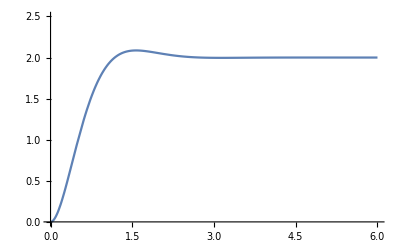

```mathematica
tr[2*Sqrt[2],Sqrt[2]/2]//N
tp[2*Sqrt[2],Sqrt[2]/2]
Mp[2*Sqrt[2],Sqrt[2]/2]//N
y[t, 2,2*Sqrt[2],Sqrt[2]/2]//FullSimplify
Plot[y[t, 2,2*Sqrt[2],Sqrt[2]/2],{t,0,6}, PlotRange->{0,2.5}]
```

```mathematica
wn[z_] := Pi/(2*Sqrt[1-z^2])
Table[{z,wn[z],z*wn[z], Sqrt[1-z^2]*wn[z]},{z,0,.99,0.1}]//TableForm
```

0. | 1.5708 | 0. | 1.5708
0.1 | 1.57871 | 0.157871 | 1.5708
0.2 | 1.60319 | 0.320637 | 1.5708
0.3 | 1.64664 | 0.493993 | 1.5708
0.4 | 1.71388 | 0.685552 | 1.5708
0.5 | 1.8138 | 0.9069 | 1.5708
0.6 | 1.9635 | 1.1781 | 1.5708
0.7 | 2.19955 | 1.53969 | 1.5708
0.8 | 2.61799 | 2.0944 | 1.5708
0.9 | 3.60365 | 3.24329 | 1.5708

```mathematica
ζ[mp_]:= Sqrt[(Log[mp]^2)/(Pi^2 +(Log[mp]^2))]
ζ[.06]
```

0.667126

```mathematica
Table[Table[{z,Wn,z*Wn, Sqrt[1-z^2]*Wn},{z,0,.7,0.1}],{Wn,0,10,.7}]
```

{{{0.,0.,0.,0.},{0.1,0.,0.,0.},{0.2,0.,0.,0.},{0.3,0.,0.,0.},{0.4,0.,0.,0.},{0.5,0.,0.,0.},{0.6,0.,0.,0.},{0.7,0.,0.,0.}},{{0.,0.7,0.,0.7},{0.1,0.7,0.07,0.696491},{0.2,0.7,0.14,0.685857},{0.3,0.7,0.21,0.667757},{0.4,0.7,0.28,0.641561},{0.5,0.7,0.35,0.606218},{0.6,0.7,0.42,0.56},{0.7,0.7,0.49,0.4999}},{{0.,1.4,0.,1.4},{0.1,1.4,0.14,1.39298},{0.2,1.4,0.28,1.37171},{0.3,1.4,0.42,1.33551},{0.4,1.4,0.56,1.28312},{0.5,1.4,0.7,1.21244},{0.6,1.4,0.84,1.12},{0.7,1.4,0.98,0.9998}},{{0.,2.1,0.,2.1},{0.1,2.1,0.21,2.08947},{0.2,2.1,0.42,2.05757},{0.3,2.1,0.63,2.00327},{0.4,2.1,0.84,1.92468},{0.5,2.1,1.05,1.81865},{0.6,2.1,1.26,1.68},{0.7,2.1,1.47,1.4997}},{{0.,2.8,0.,2.8},{0.1,2.8,0.28,2.78596},{0.2,2.8,0.56,2.74343},{0.3,2.8,0.84,2.67103},{0.4,2.8,1.12,2.56624},{0.5,2.8,1.4,2.42487},{0.6,2.8,1.68,2.24},{0.7,2.8,1.96,1.9996}},{{0.,3.5,0.,3.5},{0.1,3.5,0.35,3.48246},{0.2,3.5,0.7,3.42929},{0.3,3.5,1.05,3.33879},{0.4,3.5,1.4,3.2078},{0.5,3.5,1.75,3.03109},{0.6,3.5,2.1,2.8},{0.7,3.5,2.45,2.4995}},{{0.,4.2,0.,4.2},{0.1,4.2,0.42,4.17895},{0.2,4.2,0.84,4.11514},{0.3,4.2,1.26,4.00654},{0.4,4.2,1.68,3.84936},{0.5,4.2,2.1,3.63731},{0.6,4.2,2.52,3.36},{0.7,4.2,2.94,2.9994}},{{0.,4.9,0.,4.9},{0.1,4.9,0.49,4.87544},{0.2,4.9,0.98,4.801},{0.3,4.9,1.47,4.6743},{0.4,4.9,1.96,4.49092},{0.5,4.9,2.45,4.24352},{0.6,4.9,2.94,3.92},{0.7,4.9,3.43,3.4993}},{{0.,5.6,0.,5.6},{0.1,5.6,0.56,5.57193},{0.2,5.6,1.12,5.48686},{0.3,5.6,1.68,5.34206},{0.4,5.6,2.24,5.13248},{0.5,5.6,2.8,4.84974},{0.6,5.6,3.36,4.48},{0.7,5.6,3.92,3.9992}},{{0.,6.3,0.,6.3},{0.1,6.3,0.63,6.26842},{0.2,6.3,1.26,6.17271},{0.3,6.3,1.89,6.00982},{0.4,6.3,2.52,5.77405},{0.5,6.3,3.15,5.45596},{0.6,6.3,3.78,5.04},{0.7,6.3,4.41,4.4991}},{{0.,7.,0.,7.},{0.1,7.,0.7,6.96491},{0.2,7.,1.4,6.85857},{0.3,7.,2.1,6.67757},{0.4,7.,2.8,6.41561},{0.5,7.,3.5,6.06218},{0.6,7.,4.2,5.6},{0.7,7.,4.9,4.999}},{{0.,7.7,0.,7.7},{0.1,7.7,0.77,7.6614},{0.2,7.7,1.54,7.54443},{0.3,7.7,2.31,7.34533},{0.4,7.7,3.08,7.05717},{0.5,7.7,3.85,6.6684},{0.6,7.7,4.62,6.16},{0.7,7.7,5.39,5.4989}},{{0.,8.4,0.,8.4},{0.1,8.4,0.84,8.35789},{0.2,8.4,1.68,8.23029},{0.3,8.4,2.52,8.01309},{0.4,8.4,3.36,7.69873},{0.5,8.4,4.2,7.27461},{0.6,8.4,5.04,6.72},{0.7,8.4,5.88,5.9988}},{{0.,9.1,0.,9.1},{0.1,9.1,0.91,9.05439},{0.2,9.1,1.82,8.91614},{0.3,9.1,2.73,8.68085},{0.4,9.1,3.64,8.34029},{0.5,9.1,4.55,7.88083},{0.6,9.1,5.46,7.28},{0.7,9.1,6.37,6.4987}},{{0.,9.8,0.,9.8},{0.1,9.8,0.98,9.75088},{0.2,9.8,1.96,9.602},{0.3,9.8,2.94,9.3486},{0.4,9.8,3.92,8.98185},{0.5,9.8,4.9,8.48705},{0.6,9.8,5.88,7.84},{0.7,9.8,6.86,6.9986}}}